# Numerische Fourier-Transformation

Antjes Contribution: Ein numerisches Verfahren, in 3d mit Radialsymmetrie zu Fouriertransformieren.
Dieses wird hier gleichzeitig verglichen mit der analytischen Lösung.

```mathematica
r[x_,y_,z_]=Sqrt[x*x+y*y+z*z]
```

√(x^2+y^2+z^2)

```mathematica
(* Die uns interessierende Funktion, radialsymmetrie *)
f[r_] = D[1/(1+(1/r)^2),r]
```

2/((1+1/r^2)^2 r^3)

```mathematica
(* Das gleiche in kartesischen Koordinaten *)
f[x_,y_,z_]=Piecewise[{{f[r[x,y,z]], r[x,y,z]>0}, {0,r[x,y,z]≤ 0}}]
```

Piecewise[{{2/((x^2+y^2+z^2)^(3/2) (1+1/(x^2+y^2+z^2))^2), √(x^2+y^2+z^2)>0}, {0, True}}]

```mathematica
(* Das Piecewise stammt von Antje, um |r|=0 anzufangen. *)
```

Zum Vergleich nun das analytische Ergebnis, mit der Karbstein-Formel.

```mathematica
Integrate[r * 2/((1+1/r^2)^2 r^3) Exp[-I 2 Pi p r],{r,-∞,∞}]
```

ConditionalExpression[-ⅇ^(-2 π Abs[p]) π (-1+2 π Abs[p]),p∈Reals]

```mathematica
Integrate[r * ((2/((1+1/r^2)^2 r^3) )/.{r-> Abs[r]})Exp[-I 2 Pi p r],{r,-∞,∞}]
```

ConditionalExpression[-2 ⅈ √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},p^2 π^2] Sign[p],p∈Reals]

```mathematica
Integrate[r (f[r]HeavisideTheta[r] - f[-r]HeavisideTheta[-r])*Exp[-I p r],{r,-∞,∞}]
```

ConditionalExpression[1/2 (2 CosIntegral[(-p^4 Sign[π-2 Arg[p]])^(1/4)] (Cos[(-p^4 Sign[π-2 Arg[p]])^(1/4)] (-p^4 Sign[π-2 Arg[p]])^(1/4)+Sin[(-p^4 Sign[π-2 Arg[p]])^(1/4)])+2 ⅈ CosIntegral[ⅈ p] (p Cosh[p]+Sinh[p])+(Cosh[p]+p Sinh[p]) (π-2 ⅈ SinhIntegral[p])+(Cos[(-p^4 Sign[π-2 Arg[p]])^(1/4)]-(-p^4 Sign[π-2 Arg[p]])^(1/4) Sin[(-p^4 Sign[π-2 Arg[p]])^(1/4)]) (π-2 SinIntegral[(-p^4 Sign[π-2 Arg[p]])^(1/4)])),Im[p]<0]

```mathematica
Integrate[r (f[r]HeavisideTheta[r] + f[-r]HeavisideTheta[-r])*Exp[-I p r],{r,-∞,∞}]
```

ConditionalExpression[1/2 (-2 CosIntegral[(-p^4 Sign[π-2 Arg[p]])^(1/4)] (Cos[(-p^4 Sign[π-2 Arg[p]])^(1/4)] (-p^4 Sign[π-2 Arg[p]])^(1/4)+Sin[(-p^4 Sign[π-2 Arg[p]])^(1/4)])+2 ⅈ CosIntegral[ⅈ p] (p Cosh[p]+Sinh[p])+(Cosh[p]+p Sinh[p]) (π-2 ⅈ SinhIntegral[p])+(-Cos[(-p^4 Sign[π-2 Arg[p]])^(1/4)]+(-p^4 Sign[π-2 Arg[p]])^(1/4) Sin[(-p^4 Sign[π-2 Arg[p]])^(1/4)]) (π-2 SinIntegral[(-p^4 Sign[π-2 Arg[p]])^(1/4)])),Im[p]<0]

```mathematica
Dh[r_] = D[1/(1+(l/r)^2),r];
Integrate[r (Dh[r]HeavisideTheta[r] + Dh[-r]HeavisideTheta[-r])*Exp[-I p r],{r,-∞,∞}]
```

ConditionalExpression[1/Abs[l]l^2 (CosIntegral[-Integrate`ExponentialsDump`symb$1969345 Abs[l]] Sin[Integrate`ExponentialsDump`symb$1969345 Abs[l]]+CosIntegral[Integrate`ExponentialsDump`symb$1969345 Abs[l]] Sin[Integrate`ExponentialsDump`symb$1969345 Abs[l]]-2 Cos[Integrate`ExponentialsDump`symb$1969345 Abs[l]] SinIntegral[Integrate`ExponentialsDump`symb$1969345 Abs[l]]+Integrate`ExponentialsDump`symb$1969345 Abs[l] (Cos[Integrate`ExponentialsDump`symb$1969345 Abs[l]] CosIntegral[-Integrate`ExponentialsDump`symb$1969345 Abs[l]]+Cos[Integrate`ExponentialsDump`symb$1969345 Abs[l]] CosIntegral[Integrate`ExponentialsDump`symb$1969345 Abs[l]]+2 Sin[Integrate`ExponentialsDump`symb$1969345 Abs[l]] SinIntegral[Integrate`ExponentialsDump`symb$1969345 Abs[l]])),p==-ⅈ Integrate`ExponentialsDump`symb$1969345&&Im[l]==0&&Re[l]≠0&&Re[Integrate`ExponentialsDump`symb$1969345]>0]

Was zum Teufel ist hier los? Warum wird das Integral immer hässlicher? Diese Ergebnisse gab es auch in Calc10 noch nie (vgl. Übersicht). Wo kommen die her, woran liegt das?

```mathematica
fTilde[p_]= 2 Pi I / p  * (-ⅇ^(-Abs[p]) π (-1+Abs[p]))
```

-(2 ⅈ ⅇ^(-Abs[p]) π^2 (-1+Abs[p]))/p

```mathematica
(* Untersuchung der f[r]-Funktion mit Plots *)
```

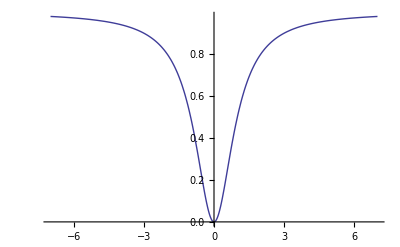

```mathematica
Plot[1/(1+(1/r)^2), {r,-7,7}]
```

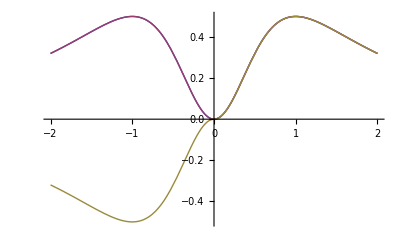

```mathematica
Plot[{r 2/((1+1/r^2)^2 r^3),r * ((2/((1+1/r^2)^2 r^3) )/.{r-> Abs[r]}),r( f[r]HeavisideTheta[r]+f[-r]HeavisideTheta[-r])},{r,-2,2}]
```

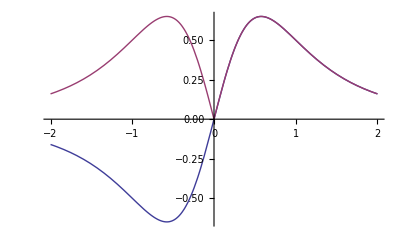

```mathematica
Plot[{2/((1+1/r^2)^2 r^3),f[r/Sqrt[3],r/Sqrt[3],r/Sqrt[3]]},{r,-2,2}]
```

```mathematica
(* f[x_] = f[x] = f[x-1] + f[x-2] ->-> Mathematica Memoization! *)
tab[n_]:=tab[n] = Table[f[x,y,z],{x,0,n},{y,0,n},{z,0,n}]
```

```mathematica
tab[3][[1,1]]
```

{0,1/2,4/25,3/50}

```mathematica
radii[n_]:=Table[r[x,y,z],{x,0,n},{y,0,n},{z,0,n}]
```

```mathematica
radii[3]
```

{{{0,1,2,3},{1,√2,√5,√10},{2,√5,2 √2,√13},{3,√10,√13,3 √2}},{{1,√2,√5,√10},{√2,√3,√6,√11},{√5,√6,3,√14},{√10,√11,√14,√19}},{{2,√5,2 √2,√13},{√5,√6,3,√14},{2 √2,3,2 √3,√17},{√13,√14,√17,√22}},{{3,√10,√13,3 √2},{√10,√11,√14,√19},{√13,√14,√17,√22},{3 √2,√19,√22,3 √3}}}

```mathematica
ListPlot3D[tab[6]]
```

-Graphics3D-

```mathematica
Manipulate[
ListPlot[{#-1,tab[n][[1,1,#]]}&  /@ Range[10],
PlotMarkers->{Automatic,Large},
Epilog->First@Plot[f[r/Sqrt[3],r/Sqrt[3],r/Sqrt[3]],{r,0,10}]
],
{n,2,15,1}]
```

Part::partd: Part specification tab[6] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification tab[6] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification tab[6] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification tab[6] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification tab[6] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification tab[6] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification tab[6] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification tab[6] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification tab[6] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

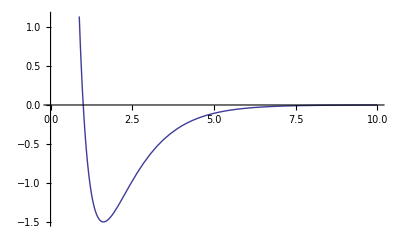

```mathematica
Plot[fTilde[p]//Im,{p,0,10}]
```

```mathematica
fTildeAnders[p_]= fTildeAnders[p]= -2 ⅈ √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},p^2 π^2]
```

-2 ⅈ √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},p^2 π^2]

```mathematica
Function[part,Manipulate[
ListPlot[{#-1,part[Fourier [tab[n]][[1,1,#]]]}&  /@ Range[10],
PlotMarkers->{Automatic,Large},
Epilog->First@Plot[fTildeAnders[r]//part,{r,0,10}]
],
{n,2,15,1}]] /@ {Re,Im}
```

{,}

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[5] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

Part::partd: Part specification Fourier[tab[5]] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 2 ⟧ is longer than depth of object.

Fourier::fftl: Argument tab[4] is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

Part::partd: Part specification Fourier[tab[4]] ⟦ 1, 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
Fourier[tab[3]] // Re // ListPlot3D
```

-Graphics3D-